Map (bin -> mode)     = {4,3,1,2}

ThetaByMode (TOTAL)   = {-65.748322,65.748322,64.463241,-64.463241}

ThetaByMode (mod 2π)  = {-2.916469,2.916469,1.631388,-1.631388}

ThetaByBin            = {-64.463241,64.463241,-65.748322,65.748322}

ThetaByBin (mod 2π)   = {-1.631388,1.631388,-2.916469,2.916469}

Dcorr diag            = {-0.0605547+0.998165 ⅈ,-0.0605547-0.998165 ⅈ,-0.974766+0.223227 ⅈ,-0.974766-0.223227 ⅈ}

||PsiFinal||          = 1.

||PsiCorrected||      = 1.

|γ| (pair 1,2) expect ≈ 1.5708

|γ| (pair 3,4) expect ≈ 1.85026

-Graphics-

-Graphics-

-Graphics-

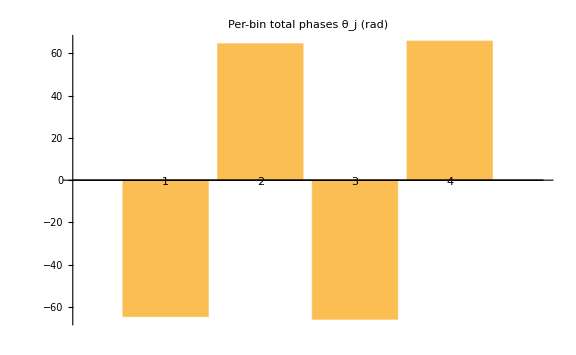

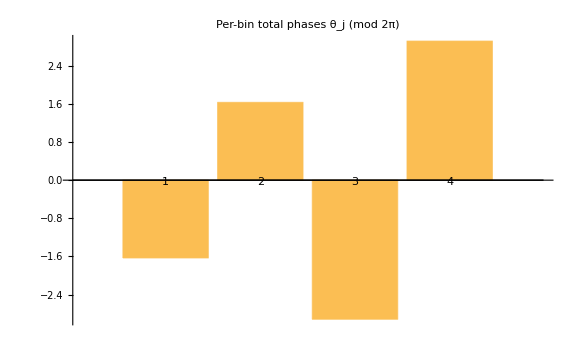

```mathematica
(* ::Package::*)(* =========================================================*)(*Time-bin Photonic Qudit:Berry/Dynamical Phases& Fix*)(*Robust state-based implementation*)(*Units:ħ=1*)(* =========================================================*)ClearAll["Global`*"];

(*----------Utilities----------*)

wrap[x_?NumericQ]:=Mod[x+Pi,2 Pi]-Pi;

normalizeSafe[v_?VectorQ]:=Module[{n=Norm[v]},If[n==0,v,v/n]];

(*Unwrapped running angle of a complex scalar;returns new (ang,acc)*)
advanceAngle[angPrev_?NumericQ,accPrev_?NumericQ,z_?NumericQ]:=Module[{a=Arg[z],step},step=wrap[a-angPrev];{a,accPrev+step}];

(*----------Hamiltonian builder:block-diagonal spins on cones----------*)

ClearAll["ExampleHamiltonianBuilder"];

ExampleHamiltonianBuilder[d_Integer,params_Association]:=Module[{BmagList,thetas=params["ThetaList"],omegas=params["OmegaList"],phases=params["PhaseOffsetList"],nb,Bvec,Hblock},nb=Floor[d/2];
BmagList=Lookup[params,"BMagList",ConstantArray[params["B0"],nb]];
Bvec[th_,om_,phi0_,Bmag_][t_]:=Bmag*{Sin[th] Cos[om t+phi0],Sin[th] Sin[om t+phi0],Cos[th]};
Hblock[vec_]:=1/2 (vec.{{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}});
Function[t,Module[{blocksAtT},blocksAtT=Table[Hblock@Bvec[thetas[[i]],omegas[[i]],phases[[i]],BmagList[[i]]][t],{i,nb}];
BlockDiagonalMatrix@Join[blocksAtT,If[OddQ[d],{{{0}}},{}]]]]]

(*----------Time-ordered unitary (piecewise-constant)----------*)

PropagatorFromH[Hfun_,t0_,T_,dt_]:=Module[{t=N@t0,U=IdentityMatrix[Length[Hfun[t0]]]},While[t<T-10^-15,U=MatrixExp[-I Hfun[t] dt].U;t+=dt;];
U]

(*----------Robust bin->mode mapping (best permutation fallback)----------*)
(*V0Cols has COLUMNS=eigenvectors at t0*)

ModeToBinMapGreedy[V0Cols_?MatrixQ]:=Module[{d=Dimensions[V0Cols][[2]],used,map,scores,idx},used=ConstantArray[False,d];map=ConstantArray[0,d];
Do[scores=Table[If[used[[k]],-Infinity,Abs[V0Cols[[j,k]]]],{k,d}];
idx=Ordering[scores,-1][[1]];used[[idx]]=True;map[[j]]=idx;,{j,d}];
map]

ModeToBinMapBest[V0Cols_?MatrixQ]:=Module[{d=Dimensions[V0Cols][[2]],perms,best},perms=Permutations[Range[Dimensions[V0Cols][[2]]]];
best=First@MaximalBy[perms,Total@Table[Abs[V0Cols[[j,#[[j]]]]],{j,d}]&];
best]

ModeToBinMap[V0Cols_?MatrixQ]:=Module[{greedy=ModeToBinMapGreedy[V0Cols],d=Dimensions[V0Cols][[2]]},If[Sort[greedy]===Range[d],greedy,ModeToBinMapBest[V0Cols]]]

(*----------State-based phases for all eigenmodes of H(t0)----------*)
(*Propagate all modes at once;columns of Psi(t) are the evolving states.*)
(*β_k(t)=unwrapped Arg[ <v_k(0)|ψ_k(t)>],ϕdyn_k=-∫⟨ψ_k|H|ψ_k⟩ dt,γ_k=β_k-ϕdyn_k*)

ClearAll["StatePhasesForModes"];
Options[StatePhasesForModes]={"hbar"->1};

StatePhasesForModes[Hfun_,t0_,T_,dt_,OptionsPattern[]]:=Module[{ħ=OptionValue["hbar"],t=N@t0,d,evals0,evecs0List,V0,Psi,dyn,beta,angPrev,logsT={},logsD={},logsG={},Ht,Ustep,overlaps,i},{evals0,evecs0List}=Eigensystem[Hfun[t0]];
V0=Transpose[evecs0List];(*columns=eigenvectors*)d=Length[evals0];
Psi=V0;(*start each mode in its eigenvector*)dyn=ConstantArray[0.,d];
beta=ConstantArray[0.,d];
angPrev=ConstantArray[0.,d];(*Arg=0 at t0 since<v(0)|ψ(0)>=1*)While[t<T-10^-15,Ht=Hfun[t];
Ustep=MatrixExp[-I Ht dt];
(*dynamical phase increment for all modes*)dyn+=-Re[Diagonal[ConjugateTranspose[Psi].(Ht.Psi)]]*dt/ħ;
(*advance Pancharatnam phases relative to initial states*)overlaps=Diagonal[ConjugateTranspose[V0].(Ustep.Psi)];
{angPrev,beta}=Transpose@MapThread[advanceAngle,{angPrev,beta,overlaps}];
Psi=Ustep.Psi;t+=dt;
AppendTo[logsD,{t,Sequence@@dyn}];
AppendTo[logsT,{t,Sequence@@beta}];
AppendTo[logsG,{t,Sequence@@(beta-dyn)}];];
<|"ThetaByMode_Total"->beta,"ThetaByMode_Dyn"->dyn,"ThetaByMode_Geom"->(beta-dyn),"V0"->V0,"LogTotalByMode"->logsT,"LogDynByMode"->logsD,"LogGeomByMode"->logsG|>]

(*----------Correction matrix----------*)

DcorrFromBinPhases[thetaByBin_List]:=DiagonalMatrix[Exp[-I thetaByBin]];

(*----------High-level wrapper----------*)

ClearAll["TimeBinQuditPhasesAndCorrection"];

TimeBinQuditPhasesAndCorrection[Hfun_,d_Integer,t0_,T_,dt_,hbar_:1,psi0_:Automatic]:=Module[{tracks,V0,mapBinToMode,thetaByMode,thetaByBin,Dcorr,U,psiInit,psiFinal,psiCorrected},tracks=StatePhasesForModes[Hfun,t0,T,dt,"hbar"->hbar];
V0=tracks["V0"];
mapBinToMode=ModeToBinMap[V0];
thetaByMode=tracks["ThetaByMode_Total"];
thetaByBin=thetaByMode[[mapBinToMode]];
Dcorr=DcorrFromBinPhases[thetaByBin];
psiInit=If[psi0===Automatic,ConstantArray[1/Sqrt[d],d],normalizeSafe[psi0]];
U=PropagatorFromH[Hfun,t0,T,dt];
psiFinal=normalizeSafe[U.psiInit];
psiCorrected=normalizeSafe[Dcorr.psiFinal];
<|"MapBinToMode"->mapBinToMode,"ThetaByMode"->thetaByMode,"ThetaByBin"->thetaByBin,"ThetaByMode_Geom"->(tracks["ThetaByMode_Geom"]),"ThetaByMode_Dyn"->(tracks["ThetaByMode_Dyn"]),"ThetaByModeMod2π"->wrap/@thetaByMode,"ThetaByBinMod2π"->wrap/@thetaByBin,"Dcorr"->Dcorr,"U"->U,"PsiInit"->psiInit,"PsiFinal"->psiFinal,"PsiCorrected"->psiCorrected,"LogTotalByMode"->tracks["LogTotalByMode"],"LogGeomByMode"->tracks["LogGeomByMode"],"LogDynByMode"->tracks["LogDynByMode"],"V0"->V0|>]

(* =====================DEMONSTRATION=====================*)

d=4;nb=Floor[d/2];

params=<|"B0"->1.0,"BMagList"->{1.0000,1.0150},(*small detuning;set both->1.0 if you want exact degeneracy*)"ThetaList"->Table[Pi/3+0.1 (i-1),{i,nb}],"OmegaList"->Table[0.05+0.01 (i-1),{i,nb}],"PhaseOffsetList"->Table[0.3 (i-1),{i,nb}]|>;

Hfun=ExampleHamiltonianBuilder[d,params];

t0=0.;T=2 Pi/params["OmegaList"][[1]];dt=0.002;ħ=1.0;

res=TimeBinQuditPhasesAndCorrection[Hfun,d,t0,T,dt,ħ];

Print["Map (bin -> mode)     = ",res["MapBinToMode"]];
Print["ThetaByMode (TOTAL)   = ",NumberForm[res["ThetaByMode"],{8,6}]];
Print["ThetaByMode (mod 2π)  = ",NumberForm[res["ThetaByModeMod2π"],{8,6}]];
Print["ThetaByBin            = ",NumberForm[res["ThetaByBin"],{8,6}]];
Print["ThetaByBin (mod 2π)   = ",NumberForm[res["ThetaByBinMod2π"],{8,6}]];
Print["Dcorr diag            = ",Diagonal[res["Dcorr"]]//Chop];
Print["||PsiFinal||          = ",Norm[res["PsiFinal"]]//N//Chop];
Print["||PsiCorrected||      = ",Norm[res["PsiCorrected"]]//N//Chop];

(*Expected|γ|for each driven pair (reference numbers)*)
expectedBerry[th_]:=Pi (1-Cos[th]);
Print["|γ| (pair 1,2) expect ≈ ",N@expectedBerry[params["ThetaList"][[1]]]];
If[nb>=2,Print["|γ| (pair 3,4) expect ≈ ",N@expectedBerry[params["ThetaList"][[2]]]]];

(*Plots*)
ListLinePlot[Evaluate@Table[res["LogTotalByMode"][[All,{1,1+k}]],{k,d}],PlotLegends->Table["total mode "<>ToString[k],{k,d}],AxesLabel->{"t","phase (rad)"},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,InterpolationOrder->1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[.85]]]

ListLinePlot[Evaluate@Table[res["LogGeomByMode"][[All,{1,1+k}]],{k,d}],PlotLegends->Table["geom mode "<>ToString[k],{k,d}],AxesLabel->{"t","phase (rad)"},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,InterpolationOrder->1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[.85]]]

ListLinePlot[Evaluate@Table[res["LogDynByMode"][[All,{1,1+k}]],{k,d}],PlotLegends->Table["dyn mode "<>ToString[k],{k,d}],AxesLabel->{"t","phase (rad)"},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,InterpolationOrder->1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[.85]]]

BarChart[res["ThetaByBin"],ChartLabels->Range[d],PlotLabel->"Per-bin total phases θ_j (rad)",ImageSize->Large]

BarChart[res["ThetaByBinMod2π"],ChartLabels->Range[d],PlotLabel->"Per-bin total phases θ_j (mod 2π)",ImageSize->Large]
```